```mathematica
Sum[x^(n*r+k)/(n*r+k)(-1)^(n*r),{n,0,Infinity}]//Simplify
```

(x^k Hypergeometric2F1[1,k/r,(k+r)/r,(-1)^r x^r])/k

```mathematica
F[z_,x_]:=Sum[(-ProductLog[-x])^k GCD[k,z] Hypergeometric2F1[1,k/z,k/z+1,(-ProductLog[-x])^z]/k,{k,1,z}]
```

```mathematica
F1[z_,x_]:=F[z,x]/(1+ProductLog[-x])
```

```mathematica
k=50;
ls=Table[SeriesCoefficient[F1[1,x],{x,0,i}]*(i!)/i^i,{i,1,k}];
```

```mathematica
Table[ls[[i]]*i^i,{i,1,50}]
```

{1,5,38,390,5049,78960,1447886,30461872,723267369,19130274880,557794986814,17775137850624,614607897664305,22917282895782912,916671255921364950,39152092883971954688,1778431981539189344177,85607684151779322519552,4353142694568849287025142,233169669255877689516032000,13122189891443883161784728457,774098864124436347645574643712,47766530309973668256839061173502,3077147548908775964879881876537344,206585423079308733608069526411625625,14430058226740689770789738807868522496,1047123450640688990929586882322998022990,78828177844283262629133248896475305345024,6148288950831510037067977404412489383405505,496238191480193571816700537727238537216000000,41399771101521090078451746497414049985779023430,3566298238118198174817891220704775697491675840512,316896884036684908906156666229005517967213388271841,29019734026569989680621784248880410620380589049511936,2736290837341881255011697574093524617090901281422343750,265438751436829102558055827208059309052863357033994256384,26470330797472327000663606905050123036318823765672297693913,2711598461219858129925839386472569886252659064981322255564800,285139367096172189097555738300453840007193939662817743418806958,30758499597484126024721476611429584080495137393650486476800000000,3401527865307292835979404568218849130920882866259477646950731876233,385409078117039661854303666105398310934976605691728598185627095138304,44715630866256975696411872968288926713932170610211299080998871263654366,5309435267650104133543977286042665570463162447212375394302400411035762688,644854341500982039763288604181210495606338848699973496672967313171994140625,80072259051179592985152423375065953087986389832812373547498014915614948196352,10160191780430387862193500813889151690710243259641832429776324448848607451285814,1316806953299637437291627901746317756420889376431884971119070922057384231044120576,174241642164063768001327303645218523942224112882769456257968303817159507605267674001,23529269379047867345281562257016282312642600366163839950425053063861753610240000000000}

```mathematica
line=Fit[ls,{1,Log[x]},x]
```

0.925422+0.436483 Log[x]

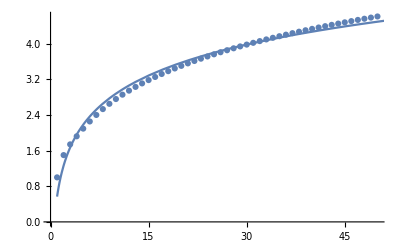

```mathematica
Show[ListPlot[ls],Plot[line,{x,1,100}]]
```

```mathematica
Table[SeriesCoefficient[F[2,x],{x,0,k}]*k!,{k,0,11}]
```

{0,1,4,23,196,2189,30336,502123,9666784,212235129,5233922560,143245937471}

```mathematica
(196Fc[1,1]+1Fc[1,4])*5+(23Fc[1,2]+4Fc[1,3])5*2
```

3060

```mathematica
n=5;
z=2;
1/(2!)Sum[Binomial[n,i](Fc[z,i]Fc[1,n-i]+Fc[z,n-i]Fc[1,i]),{i,0,n}]
```

3060

```mathematica
M[n_,k_,z_]:=1/(k!)Total@Map[(Multinomial@@#)*Sum[Fc[z,#[[i]]]*Times@@Table[Fc[1,#[[p]]],{p,Table[i,{i,Range[i-1]~Join~Range[i+1,k]}]}],{i,1,k}]&,gener[n,k]]
```

```mathematica
M[11,10,4]
```

1705

```mathematica
z=4;
n=11;
k=10;
SeriesCoefficient[1/((k-1)!)F[z,x](F[1,x])^(k-1),{x,0,n}]*n!
```

1705

```mathematica
gener[n_,k_]:=Module[{i,ls={}},
If[k==1,Return[{{n}}]];
For[i=1,i<n,i++,ls=Join[ls,Append[#,i]&/@(gener[n-i,k-1])]];
Return[ls]
]
```